```mathematica
T=100; (*максимальний час*)
S=10;(*радіус квадрата (половина сторони)*)
Du=0.01; (*просторова дифузія зайців*)
Dv=0.01;(*просторова дифузія вовків*)
ru=0.1; (*коефіцієнт безумовного росту зайців*)
rv=0.1;(*коефіцієнт безумовного росту вовків*)
auv=0.5; (*коефіцієнт впливу вовків на кількість зайців*)
avu=0.5;(*коефіцієнт впливу зайців на кількість вовків*)
auu=0.1; (*коефіцієнт ефекту надлишкової популяції зайців*)
avv=0.1; (*коефіцієнт ефекту надлишкової популяції вовків*)
(*Create initial data for u and v*)
gridPoints=5;
SeedRandom[2];
datau=Flatten[Table[{x,y,If[Abs[x]==S||Abs[y]==S,0,RandomReal[{1,2}]]},{x,-S,S,2 S/gridPoints},{y,-S,S,2 S/gridPoints}],1];
datav=Flatten[Table[{x,y,If[Abs[x]==S||Abs[y]==S,0,RandomReal[{1,2}]]},{x,-S,S,2 S/gridPoints},{y,-S,S,2 S/gridPoints}],1];
(*Create interpolating functions for initial conditions*)
initu=Interpolation[datau,Method->"Spline"];
initv=Interpolation[datav,Method->"Spline"];
```

```mathematica
sol=NDSolve[{D[u[t,x,y],t]== Du*(D[u[t,x,y],x,x]+D[u[t,x,y],y,y])+u[t,x,y]*(ru-auu*u[t,x,y]-auv*v[t,x,y]),
		       D[v[t,x,y],t]== Dv*(D[v[t,x,y],x,x]+D[v[t,x,y],y,y])+v[t,x,y]*(rv-avv*v[t,x,y]-avu*u[t,x,y]),
			u[0,x,y]==initu[x,y],v[0,x,y]==initv[x,y],
			u[t,-S,y]==0,v[t,-S,y]==0,u[t,S,y]==0,v[t,S,y]==0, (*обмеження на краях області*)
			u[t,x,-S]==0,v[t,x,-S]==0,u[t,x,S]==0,v[t,x,S]==0},
			{u,v},{t,0,T},{x,-S,S},{y,-S,S}]
```

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

```mathematica
Plot3D[Evaluate[{u[T,x,y],v[T,x,y]} /. First[sol]],
 {x,-10,10}, {y, -10, 10},PlotRange -> All,
PlotLegends->{"u (Prey)","v (Predator)"}  (*Custom legend labels*)]
```

-Graphics3D-

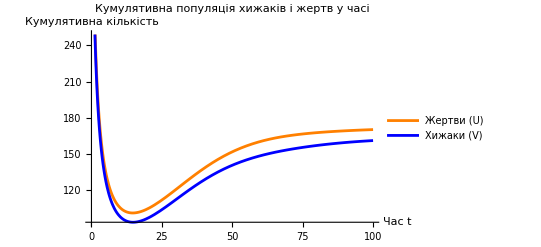

```mathematica
(*Кумулятивна кількість хижаків та жертв*)
cumulativeU[t_]:=Integrate[Evaluate[u[t,x,y]/. sol],{x,-S,S},{y,-S,S}]
cumulativeV[t_]:=Integrate[Evaluate[v[t,x,y]/. sol],{x,-S,S},{y,-S,S}]

(*Графік*)
Plot[{cumulativeU[t],cumulativeV[t]},{t,0,T},
PlotStyle->{Orange,Blue},
PlotLegends->{"Жертви (U)","Хижаки (V)"},
AxesLabel->{"Час t","Кумулятивна кількість"},
PlotLabel->"Кумулятивна популяція хижаків і жертв у часі"]
```